Yohan Lee Lab 8

Examples

```mathematica
s[n_]:=Sum[1/k,{k,1,n}]
```

```mathematica
Function[n,∑_(k=1)^n 1/k]
```

Function[n,∑_(k=1)^n 1/k]

```mathematica
vals=Table[{n,s[n]},{n,1,101}];
```

```mathematica
vals[[;; ;; 10]]//N//TableForm
```

1. | 1.
11. | 3.01988
21. | 3.64536
31. | 4.02725
41. | 4.30293
51. | 4.51881
61. | 4.69626
71. | 4.84692
81. | 4.97782
91. | 5.09356
101. | 5.19728

```mathematica
vals2=Table[{n,s[n]},{n,1,101,10}]//N//TableForm
```

1. | 1.
11. | 3.01988
21. | 3.64536
31. | 4.02725
41. | 4.30293
51. | 4.51881
61. | 4.69626
71. | 4.84692
81. | 4.97782
91. | 5.09356
101. | 5.19728

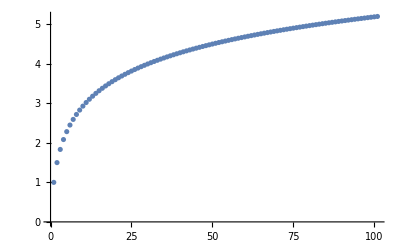

```mathematica
ListPlot[vals]
```

```mathematica
s[Infinity]
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ 1/k

Question 1

a)

```mathematica
Clear[s,vals];
s[n_]:=Sum[1/k^2,{k,1,n}];
vals=Table[{n,s[n]},{n,1,101}];
vals[[;; ;; 10]]//N//TableForm
```

1. | 1.
11. | 1.55803
21. | 1.59843
31. | 1.61319
41. | 1.62084
51. | 1.62552
61. | 1.62867
71. | 1.63095
81. | 1.63266
91. | 1.63401
101. | 1.63508

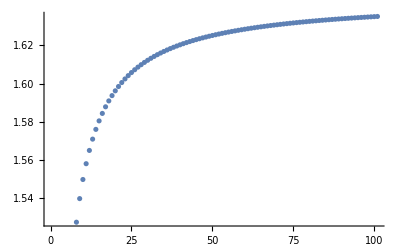

```mathematica
ListPlot[vals]
```

```mathematica
s[Infinity]
```

π^2/6

Converges to

```mathematica
s[Infinity]//N
```

1.64493

b)

```mathematica
Clear[s,vals];
s[n_]:=Sum[Log[k]/k^2,{k,1,n}];
vals=Table[{n,s[n]},{n,1,1001}];
vals[[;; ;; 100]]//N//TableForm
```

1. | 0.
101. | 0.882179
201. | 0.906254
301. | 0.915297
401. | 0.920126
501. | 0.923156
601. | 0.925247
701. | 0.926781
801. | 0.927958
901. | 0.928892
1001. | 0.929651

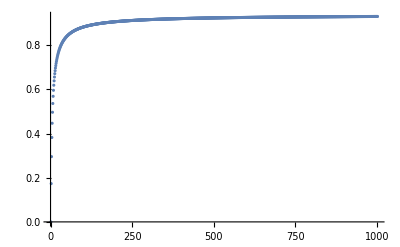

```mathematica
ListPlot[vals]
```

```mathematica
s[Infinity]
```

-1/6 π^2 (EulerGamma+Log[2]-12 Log[Glaisher]+Log[π])

Converges to

```mathematica
s[Infinity]//N
```

0.937548

c)

```mathematica
Clear[s,vals];
s[n_]:=Sum[1/Factorial[k],{k,0,n}];
vals=Table[{n,s[n]},{n,1,20}];
vals[[;; ;; 2]]//N//TableForm
```

1. | 2.
3. | 2.66667
5. | 2.71667
7. | 2.71825
9. | 2.71828
11. | 2.71828
13. | 2.71828
15. | 2.71828
17. | 2.71828
19. | 2.71828

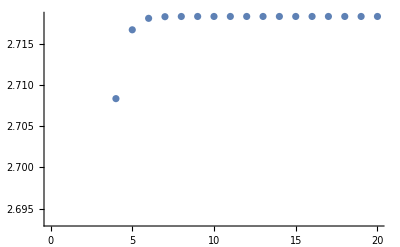

```mathematica
ListPlot[vals]
```

```mathematica
s[Infinity]
```

ⅇ

Converges to

```mathematica
s[Infinity]//N
```

2.71828

Question 2

```mathematica
t[n_]:=Sum[1/Factorial[k],{k,0,n}]
```

```mathematica
Function[n,∑_(k=0)^n 1/(k!)]
```

Function[n,∑_(k=0)^n 1/(k!)]

```mathematica
errors={}
```

{}

```mathematica
exact=Exp[1]
```

ⅇ

```mathematica
For[m=1,m≤10,m++,errors=Append[errors,Abs[t[m]-exact]]]
```

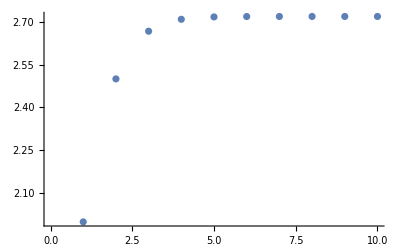

```mathematica
ListPlot[Table[{n,t[n]},{n,1,10}]]
```

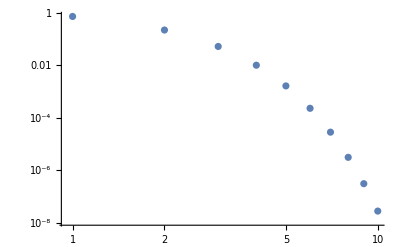

```mathematica
ListLogLogPlot[errors]
```

Observations

The error decreases with subsequent values of the partial sum t[n]. The partial sums are a good approximation of e.

Question3

```mathematica
f[n_]:=Sum[1/k^2,{k,1,n}]
```

```mathematica
Function[n,∑_(k=1)^n 1/k^2]
```

Function[n,∑_(k=1)^n 1/k^2]

```mathematica
errs={}
```

{}

```mathematica
exact=Pi^2/6
```

π^2/6

```mathematica
For[m=1,m≤10,m++,errs=Append[errs,Abs[f[m]-exact]]]
```

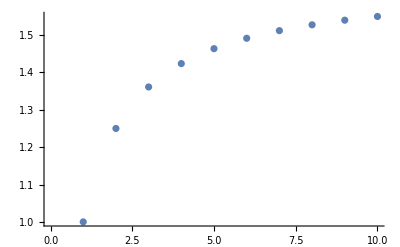

```mathematica
ListPlot[Table[{n,f[n]},{n,1,10}]]
```

```mathematica
exact//N
```

1.64493

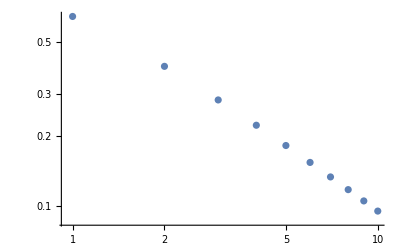

```mathematica
ListLogLogPlot[errs]
```

Observations

The error decreases with subsequent values of the partial sum f[n]. The partial sums are a good approximation of π^2/6.